## Sample generation :

```mathematica
(* 0 Define variables*)
SetDirectory[NotebookDirectory[]];
$HistoryLength = 0;

N1=3;N2=3; degX=3; degY=3; 
variX=Table[Subscript[x,n],{n,0,N1-1}];
variY=Table[Subscript[y,n],{n,0,N2-1}];
variXC=Table[Subscript[OverBar[x],n],{n,0,N1-1}];
variYC=Table[Subscript[OverBar[y],n],{n,0,N1-1}];
vari=Join[variX,variY]; variC=Join[variXC,variYC];
complexConjugate = Join[Thread[vari -> variC], Thread[variC -> vari]];
dimP=3;npA=Length[vari]-2; npX=npA-1;

tuples=Tuples[{variX,variY}]; numpp=Length[tuples];
patches=Table[{tuples[[i]][[1]]->1,tuples[[i]][[2]]->1},{i,1,Length[tuples]}];
redunC=Table[1,{i,1,numpp}];
inhomoCors=Table[RotateRight[Complement[vari, tuples[[pth]]],npA-redunC[[pth]]],{pth,1,Length[tuples]}];
CinhomoCors=inhomoCors/.complexConjugate;
Print["The redundent coordinates on every patch are "<>ToString[redunC]];

(* possible symmetries *)
findRep[element_,basis_List]:=Module[{vari,as,genSec,tt},
vari=Variables[basis];
as=Table[Subscript[a, i],{i,1,Length[basis]}];
genSec=as.basis;
tt=DeleteCases[Flatten[CoefficientList[element-genSec,vari]],0];
Solve[Table[tt[[i]]==0,{i,1,Length[tt]}],as][[1]]/.Rule->(#2&)];

α=Exp[I 2 Pi/3];
rep1={Subscript[x, 0]->Subscript[x, 1],Subscript[x, 1]->Subscript[x, 2],Subscript[x, 2]->Subscript[x, 0],Subscript[y, 0]->Subscript[y, 1],Subscript[y, 1]->Subscript[y, 2],Subscript[y, 2]->Subscript[y, 0]};

rep2={Subscript[x, 0]->Subscript[x, 0],Subscript[x, 1]->α Subscript[x, 1],Subscript[x, 2]->α^2 Subscript[x, 2],Subscript[y, 0]->Subscript[y, 0],Subscript[y, 1]->α ^(-1)Subscript[y, 1],Subscript[y, 2]->α^(-2) Subscript[y, 2]};

tvari1=vari/.rep1;tvari2=vari/.rep2;
sym1=Table[findRep[tvari1[[i]],vari],{i,1,Length[tvari1]}];
sym2=Table[findRep[tvari2[[i]],vari],{i,1,Length[tvari2]}];
Print[MatrixForm[sym1]];
Print[MatrixForm[sym2]];

MonoList[vari_List,Pnum_Integer]:=Module[{tp,mono,coefmono,pt,outp},pt=Abs[Pnum];tp=(Total[vari])^pt;
mono=MonomialList[tp];
coefmono=mono/.Thread[vari->Table[1,{i,1,Length[vari]}]];
outp=mono/coefmono;
If[Pnum≥0,outp,{}]];
findInvZ3[monos_]:=Module[{index},
DeleteCases[Table[If[monos[[i]]-(monos[[i]]/.rep2)===0,monos[[i]],0],{i,1,Length[monos]}],0]
];

sAction1[p_]:=p/.rep1;
findInvZ3perm[monos_]:=Module[{},
Union[Table[Total[Union[NestList[sAction1,monos[[i]],2]]],{i,1,Length[monos]}]]];

monoX=MonoList[variX,degX];monoY=MonoList[variY,degY];
monos=Flatten[Outer[Times,monoX,monoY]];
Print[{"# of monos ",Length[monos]}];
invMonos=findInvZ3perm[findInvZ3[monos]];
Print[{"# of Z3Z3 inv monos ",Length[invMonos]}];

defCoffs=RandomInteger[{-5,10},12];
defCoffs={1,1,1,2,0,1,-1,3,-1,1,0,-1};
DefPoly=invMonos.defCoffs;
(*ps=2;
DefPoly=invMonos[[9]]+invMonos[[10]]+invMonos[[12]]+ps*invMonos[[1]]; *)
Print[DefPoly];
```

The redundent coordinates on every patch are {1, 1, 1, 1, 1, 1, 1, 1, 1}

(0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 1 | 0 | 0)

(1 | 0 | 0 | 0 | 0 | 0
0 | (-1)^(2/3) | 0 | 0 | 0 | 0
0 | 0 | -(-1)^(1/3) | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | -(-1)^(1/3) | 0
0 | 0 | 0 | 0 | 0 | (-1)^(2/3))

{# of monos ,100}

{# of Z3Z3 inv monos ,12}

-x_0^3 y_0^3-x_1^3 y_0^3+x_2^3 y_0^3+x_1^2 x_2 y_0^2 y_1+x_0^2 x_2 y_0 y_1^2-x_1 x_2^2 y_0 y_1^2+x_0^3 y_1^3-x_1^3 y_1^3-x_2^3 y_1^3-x_0 x_1^2 y_0^2 y_2+x_1 x_2^2 y_0^2 y_2+x_0^3 y_0 y_1 y_2+x_1^3 y_0 y_1 y_2+x_0 x_1 x_2 y_0 y_1 y_2+x_2^3 y_0 y_1 y_2+x_0 x_2^2 y_1^2 y_2+x_0^2 x_1 y_0 y_2^2+x_0 x_1^2 y_1 y_2^2-x_0^2 x_2 y_1 y_2^2-x_0^3 y_2^3+x_1^3 y_2^3-x_2^3 y_2^3+2 (x_0 x_2^2 y_0^2 y_1+x_0^2 x_1 y_1^2 y_2+x_1^2 x_2 y_0 y_2^2)+3 (x_0 x_1^2 y_0 y_1^2+x_0^2 x_2 y_0^2 y_2+x_1 x_2^2 y_1 y_2^2)

```mathematica
numPoint=1000; cl=0.01;
nameSample="Sample"<>ToString[numPoint];
nameMass="Mass"<>ToString[numPoint];
gnumPoint=numPoint*Length[patches];
```

```mathematica
nP=2;
varis={variX,variY};
variNs=Length/@varis; 
repPatch=Join[Thread[variX->{1,2,3}],Thread[variY->{1,2,3}]];
namePatch=tuples/.repPatch;

(* 1. generate the uniformly distributed points on the n-sphere (norm distribution) *)
normS[m_]:=m/Norm[m];
complexifyP[m_]:=Complex@@@Partition[m,2];
spherePt[nCor_,numPoint_]:=Module[{ptS},
ptS=complexifyP/@normS/@Transpose[Table[RandomVariate[NormalDistribution[0,1],numPoint*(Length[patches]+1)],{i,1,nCor*2}]];
ptS];

(* 2. generate the intersection points on the calabi-yau manifold *)
interCY2[numP_,ptS_]:=Module[{tpoints,rep,m,t,tDefPoly},
tpoints=Flatten/@Table[If[i==numP,m=RandomChoice[ptS[[i]],2];m[[1]]+t*m[[2]],RandomChoice[ptS[[i]],1]],{i,1,nP} ];
rep=Flatten[Table[Thread[varis[[i]]->tpoints[[i]]],{i,1,nP}]];
tDefPoly=DefPoly/.rep;
tpoints/.Solve[tDefPoly==0,t]
];

(* 3. reform the data and make sure that every patch has the same number of data *)
patchCors[m_List]:=Module[{tm,ttm,j},
j=0;
Flatten[Table[ttm=m[[j+1;;j+variNs[[i]]]];
j=j+variNs[[i]];
tm=Abs[ttm];Position[tm,Max[tm]],{i,1,nP}]]];

HICComplex=Table[{#, _Complex} & /@ inhomoCors[[pth]],{pth,1,Length[patches]}];
(* Find the CF of Q *)
getfuncQaRedun[pth_Integer]:=Module[{DefPolyl,Qa},
DefPolyl=DefPoly/.patches[[pth]];
Qa=D[DefPolyl,{inhomoCors[[pth,npA]]}];
Compile[Evaluate[ HICComplex[[pth]] ], Evaluate[Qa]
(*,CompilationTarget->"C",RuntimeOptions->"Speed",RuntimeAttributes->Listable,Parallelization->True*)
]];
funcQaRedun=Table[getfuncQaRedun[pth],{pth,1,Length[patches],1}];

(* 4.Project global points to local points on patches *)
glob2loc[pth_,CYpoints_,redunC_]:=Module[{tCYpointsl,tt,ttm,ttt,indP,j,shift},

tt=Transpose[CYpoints];
shift=npA-redunC[[pth]];

j=0;
ttt=Transpose[RotateRight[Flatten[
Table[ttm=tt[[j+1;;j+variNs[[i]]]];
j=j+variNs[[i]]; indP=namePatch[[pth,i]]; 
(* delete the patch coordinates *)
Delete[Table[ttm[[i]]/ttm[[indP]],{i,1,variNs[[i]]}],indP]
,{i,1,nP}],1],shift]]
];

(*5 Check the accuracy of sample using local points*)
TestCYSampleLoc[ptCY_List,pth_Integer]:=Module[{rep},
rep=Join[patches[[pth]],Thread[inhomoCors[[pth]]->ptCY]];
Abs[DefPoly/.rep]];

getSample[numPoint_]:=Module[{ptS,gCYpts,inx,indexL,lCYpts,CYpointsl,errs},

(* 1. generate the uniformly distributed points on the n-sphere (norm distribution) *)
ptS=Table[spherePt[variNs[[i]],numPoint],{i,1,2}];
Print["Generate points in Disk before intersection  "<>ToString[Length/@ptS]];

(* 2. generate the intersection points on the calabi-yau manifold *)
gCYpts=Flatten[ParallelTable[
Flatten/@interCY2[i,ptS],{i,1,nP},{j,1,Floor[numPoint*Length[tuples]]/3/2*1.2}],2];
Print["We generate global points with number "<>ToString[Dimensions[gCYpts]]];

(* 3. reform the data and make sure that every patch has the same number of data *)
inx=patchCors/@gCYpts;
indexL=Table[Flatten[Position[inx,namePatch[[i]]]],{i,1,Length[tuples]}];
If[Min[Length/@indexL]<numPoint,Print["Error"];Exit[];];
(*N[Max[ttt]/Min[ttt]]*)
lCYpts=Table[gCYpts[[indexL[[i,j]]]],{i,1,Length[tuples]},{j,1,Length[indexL[[i]]]}];
Print["We generate sample with number "<>ToString[Length/@indexL]];

(* 4.Project global points to local points on patches *)
tCYpointsl=ParallelTable[glob2loc[pth,lCYpts[[pth]],redunC],{pth,1,Length[patches]}];
Print["We get sample points " <> ToString[Length/@tCYpointsl]];
(* make sure the points are not close to singular region *)
CYpointsl=ParallelTable[Select[tCYpointsl[[pth]],Abs[funcQaRedun[[pth]]@@#]^2>cl&,numPoint],{pth,1,Length[patches]}];
Print["We get sample points " <> ToString[Dimensions[CYpointsl]]];

(*5 Check the accuracy of sample using local points*)
errs=Table[TestCYSampleLoc[CYpointsl[[pth,pt]],pth],{pth,1,Length[tuples]},{pt,1,numPoint}];
Print[ListPlot[Flatten[errs]]];
CYpointsl
];
```

Generate points in Disk before intersection  {10000, 10000}

We generate global points with number {10800, 6}

We generate sample with number {1119, 1335, 1227, 1206, 1136, 1292, 1185, 1223, 1077}

We get sample points {1119, 1335, 1227, 1206, 1136, 1292, 1185, 1223, 1077}

We get sample points {9, 1000, 4}

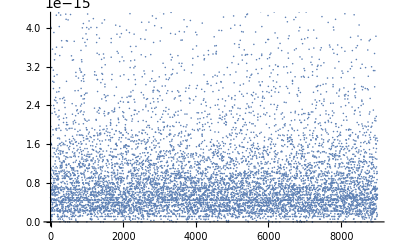

```mathematica
CYpointsl=getSample[numPoint];
Export[ nameSample,Flatten[CYpointsl,1], {"Binary", "Complex128"}];
```

#### Compute the mass:

```mathematica
(* Kahler potential for FS metric *)
Kx=Log[Total[variX*variXC]];
Ky=Log[Total[variY*variYC]];
K=Kx+Ky; 
patchesC=patches/.complexConjugate;
patchesT=Table[Join[patches[[i]],patchesC[[i]]],{i,1,Length[patches]}];

HICComplex=Table[{#, _Complex} & /@ inhomoCors[[pth]],{pth,1,Length[patches]}];
conj = Table[Thread[ CinhomoCors[[pth]] -> Conjugate[inhomoCors[[pth]] ] ],{pth,1,Length[patches]}];
(* Find the CF of Q *)
getfuncQa[pth_Integer]:=Module[{DefPolyl,Qa},
DefPolyl=DefPoly/.patches[[pth]];
Qa=D[DefPolyl,{inhomoCors[[pth]]}];
Compile[Evaluate[ HICComplex[[pth]] ], Evaluate[Qa]
(*,CompilationTarget->"C",RuntimeOptions->"Speed",RuntimeAttributes->Listable,Parallelization->True*)
]];
funcQa=Table[getfuncQa[pth],{pth,1,Length[patches],1}];

(* Find the CF of Kx *)
getfuncK[pth_Integer]:=Module[{Kl,JAab},
Kl = K/.patchesT[[pth]];
JAab=D[D[Kl,{inhomoCors[[pth]]}],{CinhomoCors[[pth]]}];
	Compile[Evaluate[ HICComplex[[pth]] ], Evaluate[JAab/.conj[[pth]]]]];
funcK=Table[getfuncK[pth],{pth,1,Length[patches]}];
	
(*Print["comm_shared_data"];time=SessionTime[];*)
DistributeDefinitions[funcK,funcQa];
(*Print[{"comm_data_done!",N[SessionTime[]-time]}];*)


gA2X[JA_,Qa_]:=Module[{tQa},
tQa=Delete[Qa/Qa[[npA]],npA];
Table[JA[[i,j]]-JA[[i,npA]]*Conjugate[tQa[[j]]]-tQa[[i]]*JA[[npA,j]]+tQa[[i]]*JA[[npA,npA]]*Conjugate[tQa[[j]]],{i,1,npX},{j,1,npX}]];

massG[CYpointsl_]:=Module[{mass,tmass,pth,JaA,Qa,point}, 

mass={};
For[pth=1,pth≤Length[tuples],pth++,
timeM=SessionTime[];
tmass=ParallelTable[
point=CYpointsl[[pth,pt]];
JaA=funcK[[pth]]@@point;
Qa=funcQa[[pth]]@@point;
Re[1.0/(Det[gA2X[JaA,Qa]]*Abs[Qa[[npA]]]^2)]
,{pt,1,numPoint,1}];
Print[{pth,N[SessionTime[]-timeM]}];
mass=Join[mass,tmass];];
mass];
```

```mathematica
mass=massG[CYpointsl]/N[gnumPoint];
Print[Dimensions[mass]];
volCY=Total[Flatten[mass]];
Print[{"The volumn of X is ",volCY}];
Export[ nameMass,Flatten[mass,1], {"Binary", "Real128"}];
```

{1,1.65927}

{2,1.67659}

{3,1.52711}

{4,1.59946}

{5,1.59061}

{6,1.61524}

{7,1.67263}

{8,1.76404}

{9,1.51578}

{9000}

{The volumn of X is ,0.5764}

## Donaldson' s algorithm :

#### 0. Manifold & Sample

```mathematica
N1=3;N2=3; 
variX=Table[Subscript[x,n],{n,0,N1-1}];
variY=Table[Subscript[y,n],{n,0,N2-1}];
variXC=Table[Subscript[OverBar[x],n],{n,0,N1-1}];
variYC=Table[Subscript[OverBar[y],n],{n,0,N1-1}];
vari=Join[variX,variY]; variC=Join[variXC,variYC];
complexConjugate = Join[Thread[vari -> variC], Thread[variC -> vari]];
dimP=3;npA=Length[vari]-2; npX=npA-1;

tuples=Tuples[{variX,variY}]; numpp=Length[tuples];
patches=Table[{tuples[[i]][[1]]->1,tuples[[i]][[2]]->1},{i,1,Length[tuples]}];
redunC=Table[1,{i,1,numpp}];
inhomoCors=Table[RotateRight[Complement[vari, tuples[[pth]]],npA-redunC[[pth]]],{pth,1,Length[tuples]}];
CinhomoCors=inhomoCors/.complexConjugate;
(*Print["The redundent coordinates on every patch are "<>ToString[redunC]];*)

(* possible symmetries *)
findRep[element_,basis_List]:=Module[{vari,as,genSec,tt},
vari=Variables[basis];
as=Table[Subscript[a, i],{i,1,Length[basis]}];
genSec=as.basis;
tt=DeleteCases[Flatten[CoefficientList[element-genSec,vari]],0];
Solve[Table[tt[[i]]==0,{i,1,Length[tt]}],as][[1]]/.Rule->(#2&)];

α=Exp[I 2 Pi/3];
rep1={Subscript[x, 0]->Subscript[x, 1],Subscript[x, 1]->Subscript[x, 2],Subscript[x, 2]->Subscript[x, 0],Subscript[y, 0]->Subscript[y, 1],Subscript[y, 1]->Subscript[y, 2],Subscript[y, 2]->Subscript[y, 0]};
rep2={Subscript[x, 0]->Subscript[x, 0],Subscript[x, 1]->α Subscript[x, 1],Subscript[x, 2]->α^2 Subscript[x, 2],Subscript[y, 0]->Subscript[y, 0],Subscript[y, 1]->α ^(-1)Subscript[y, 1],Subscript[y, 2]->α^(-2) Subscript[y, 2]};

tvari1=vari/.rep1;tvari2=vari/.rep2;
sym1=Table[findRep[tvari1[[i]],vari],{i,1,Length[tvari1]}];
sym2=Table[findRep[tvari2[[i]],vari],{i,1,Length[tvari2]}];
(*Print[MatrixForm[sym1]];
Print[MatrixForm[sym2]];*)

MonoList[vari_List,Pnum_Integer]:=Module[{tp,mono,coefmono,pt,outp},pt=Abs[Pnum];tp=(Total[vari])^pt;
mono=MonomialList[tp];
coefmono=mono/.Thread[vari->Table[1,{i,1,Length[vari]}]];
outp=mono/coefmono;
If[Pnum>=0,outp,{}]];
findInvZ3[monos_]:=Module[{index},
DeleteCases[Table[If[monos[[i]]-(monos[[i]]/.rep2)===0,monos[[i]],0],{i,1,Length[monos]}],0]
];

sAction1[p_]:=p/.rep1;
findInvZ3perm[monos_]:=Module[{},
Union[Table[Total[Union[NestList[sAction1,monos[[i]],2]]],{i,1,Length[monos]}]]];

degX=3; degY=3; 
monoX=MonoList[variX,3];monoY=MonoList[variY,3];
monos=Flatten[Outer[Times,monoX,monoY]];
(*Print[{"# of monos ",Length[monos]}];*)
invMonos=findInvZ3perm[findInvZ3[monos]];
(*Print[{"# of Z3Z3 inv monos ",Length[invMonos]}];*)
defCoffs=RandomInteger[{-5,10},12];
defCoffs={1,1,1,2,0,1,-1,3,-1,1,0,-1};
DefPoly=invMonos.defCoffs;
(*Print[DefPoly];*)

(*Check O(1,1) is equivariant under Z3Z3*)
H0L=Apply[Times,Tuples[{variX,variY}],1]; 
tvari1=H0L/.rep1;tvari2=H0L/.rep2;
sym1=Table[findRep[tvari1[[i]],H0L],{i,1,Length[tvari1]}];
sym2=Table[findRep[tvari2[[i]],H0L],{i,1,Length[tvari2]}];

(*2 Read the data from files *)
getPointsFile[filename_String] := Module[{stream},
           stream = OpenRead[ filename, BinaryFormat -> True ];
          Partition[
                 BinaryReadList[ stream, "Complex128" ], npA]];

getPointsFile2[filename_String] := Module[{stream},
           stream = OpenRead[ filename, BinaryFormat -> True ];
      BinaryReadList[ stream, "Real128" ]];
      
indexData[numCY_List,numpp_Integer]:=Module[{tcount},tcount=0;
	Join[{0},Table[tcount+=numCY[[pth]],{pth,1,numpp-1,1}]]];
```

#### 1. Global sections & Prepare the data

```mathematica
MonoList[vari_List,Pnum_Integer]:=Module[{tp,mono,coefmono,pt,outp},pt=Abs[Pnum];tp=(Total[vari])^pt;
mono=MonomialList[tp];
coefmono=mono/.Thread[vari->Table[1,{i,1,Length[vari]}]];
outp=mono/coefmono;
If[Pnum>=0,outp,{}]];

CoeffFromMonos[m_List,monos_List]:=Module[{tcoflist,ttm,i,j,zeroB},zeroB={};
For[j=1,j<=Length[m],j++,tcoflist={};
For[i=1,i<=Length[monos],i++,ttm=Coefficient[m[[j]],monos[[i]]];
AppendTo[tcoflist,ttm]];
AppendTo[zeroB,tcoflist];];
Return[zeroB]];

H0Xs2[k_Integer,Monos_,cs_]:=Module[{monoX3,monoY3,monos3,Mt,Mt2,tk,tMonos,zeros,zeroBasis,q,qBasis},
If[k<3,Return[IdentityMatrix[Length[Monos]]];];tk=k-3;
(* find invariant sections *)
monoX3=MonoList[variX,tk];monoY3=MonoList[variY,tk];
monos3=Flatten[Outer[Times,monoX3,monoY3]];
tMonos=findInvZ3perm[findInvZ3[monos3]];
zeros=cs*tMonos;
(*Print[Length[zeros]];*)
zeroBasis=CoeffFromMonos[zeros,Monos];
NullSpace[zeroBasis]];

(* 1 invariant basis of C on X *)
monoX=MonoList[variX,k];monoY=MonoList[variY,k];
tmonos=Flatten[Outer[Times,monoX,monoY]];
(*Print[{"# of monos ",Length[tmonos]}];*)
monos=findInvZ3perm[findInvZ3[tmonos]]; 
(*Print["The Z5*Z5 invariant global sections on A: "<>ToString[Length[monos]]];*)

(* Take the first mono as the rep of the poly *)
repMonos=Table[MonomialList[monos[[i]]][[1]],{i,1,Length[monos]}]; 
invqBasis=H0Xs2[k,repMonos,DefPoly].monos;qh0=Length[invqBasis];
Print["The Z5*Z5 invariant global sections on X: "<>ToString[qh0]];
indL=(k^3+2*k)/3;
Print[{"The Z5Z5 invariant global sections from index theorem for cross check: ",indL}];

HICComplex=Table[{#, _Complex} & /@ inhomoCors[[pth]],{pth,1,Length[patches]}];
(* Find the CF of Q *)
getfuncQa[pth_Integer]:=Module[{DefPolyl,Qa},
DefPolyl=DefPoly/.patches[[pth]];
Qa=D[DefPolyl,{inhomoCors[[pth]]}];
Compile[Evaluate[ HICComplex[[pth]] ], Evaluate[Qa]
(*,CompilationTarget->"C",RuntimeOptions->"Speed",RuntimeAttributes->Listable,Parallelization->True*)
]];
funcQa=Table[getfuncQa[pth],{pth,1,Length[patches],1}];

(* Find the CF of s *)
getfuncS[pth_Integer]:=Module[{DefPolyl,qBasisl},
qBasisl = invqBasis/.patches[[pth]];
Compile[Evaluate[ HICComplex[[pth]] ], Evaluate[qBasisl]]];
funcS=Table[getfuncS[pth],{pth,1,Length[patches]}];

(* Find the CF of ds *)
genfuncSd[pth_Integer]:=Module[{qBasisl,dqBasisl},
qBasisl = invqBasis/.patches[[pth]];
dqBasisl=D[qBasisl, {inhomoCors[[pth]]}];
Compile[Evaluate[HICComplex[[pth]]], 
Evaluate[dqBasisl]
(*,CompilationTarget->"C",RuntimeOptions->"Speed",RuntimeAttributes->Listable,Parallelization->True*)]
];
funcSd=Table[genfuncSd[pth],{pth,1,Length[patches]}];

(*Print["comm_shared_data"];time=SessionTime[];*)
DistributeDefinitions[funcS,funcQa,funcSd];
```

#### 2. T - operator :

```mathematica
getH[filename_String] := Module[{stream},
         stream = OpenRead[ filename, BinaryFormat -> True ];
   Partition[BinaryReadList[ stream, "Complex128" ], qh0]
        ];

getT2=Compile[{{s,_Complex,1},{H,_Complex,2}}, Module[{cs,InG,qh0,iP},
qh0=Length[s];
cs=Conjugate[s];
iP =cs.H.s;
Table[s[[A1]]*cs[[B1]], {A1, 1, qh0}, {B1, 1, qh0}]/iP
]
(*,CompilationTarget->"C"
,RuntimeOptions->"Speed",RuntimeAttributes->Listable,Parallelization->True*)];

Toperator[H_] := Module[{},
	ParallelEvaluate[tT=ConstantArray[0.,{qh0,qh0}];];
	lnH=Inverse[H];DistributeDefinitions[lnH];
	Table[
	DistributeDefinitions[pth];
	ParallelTable[
		point=CYpoints[[pt]];
		tT+=getT2[funcS[[pth]]@@point,lnH]*massCY[[pt]];
	,{pt,count[[pth]]+1,count[[pth]]+numCY[[pth]],1},
	Method->"CoarsestGrained",DistributedContexts->None];
	(*Print[{pth,Total[ParallelEvaluate[tT]]}];*)
,{pth,1,Length[patches]}];
N[qh0*Total[ParallelEvaluate[tT]]/volCY]];

eigenQ2[h1_,h2_] := Module[{e1,e2},
	e1=Max[Abs[Eigenvalues[h1]]];
	e2=Max[Abs[Eigenvalues[h2]]];
	Abs[(e1/e2)-1.0]];
	
iterT[Hth_Integer,Hp0_, nIter_Integer, nSaveH_Integer,nameH_,numPoint_,nameS_,nameW_]:=Module[{st,H,timeM,tH,errT},
	
	CYpoints=getPointsFile[nameS];gnumPoint=Length[CYpoints];
	massCY =Re[ getPointsFile2[nameW]];
	volCY=Total[massCY]; 
	numCY = If[numPoint==0,IntegerPart[Re[getPointsFile2[nameN]]],ConstantArray[numPoint,Length[patches]]];
	count=indexData[numCY,Length[patches]];
	Print["2a) We get sample "<>ToString[gnumPoint]];
	Print[numCY];
	Print[{"The volumn is ",volCY}];
	
	(*Print["comm_shared_data"];time=SessionTime[];*)
	DistributeDefinitions[CYpoints,massCY,count,numCY,qh0,npA,npX];
	DistributeDefinitions[getT2];
	(*Print[{"comm_data_done!",N[SessionTime[]-time]}];
*)
	For[st =Hth;H = Hp0, st <= nIter, st++,
		timeM = SessionTime[];
		tH = Toperator[H]; 
		errT = eigenQ2[tH, H]; H=tH;
		Print[{st, errT, N[SessionTime[] - timeM]}];
		If[Mod[st,nSaveH]==0,Export[ nameH<>ToString[st], H , {"Binary", "Complex128"}]];
	];
];
```

#### 3. Evaluate the Error

```mathematica
dA2X[m_,Qa_]:=Table[m[[i]]-(Qa[[i]]/Qa[[npA]])*m[[npA]],{i,1,npX,1}];

getM2[Qa_,gs_,ds_,H_]:=Module[{cgs,dgs,cdgs,i,j,ts,InG,dG,cdG,ddG,Mb,tM,M,gij},
(* H: 1st is anti; 2nd is homo *)
cgs=Conjugate[gs];  
dgs=Transpose[Table[dA2X[ds[[i]],Qa],{i,1,qh0}]]; 
cdgs=Conjugate[dgs];

InG=cgs.H.gs;
dG=Table[cgs.H.dgs[[a]],{a,1,npX}];
cdG=Table[cdgs[[b]].H.gs,{b,1,npX}];
ddG=Table[cdgs[[b]].H.dgs[[a]],{a,1,npX},{b,1,npX}];
Mb=Table[cdG[[b]]*dG[[a]]/InG,{a,1,npX},{b,1,npX}];
gij=N[(ddG-Mb)/InG/k];
gij
];

getNmetric[H_] :=Module[ {pth,pt,tnmetric,nmetric,point,data,tJw,time},

(*Print["comm_shared_data"];time=SessionTime[];*)
DistributeDefinitions[dA2X,getM2];
(*Print[{"comm_data_done!",N[SessionTime[]-time]}];*)

nmetric={};

For[pth=1,pth<=Length[patches],pth++,

DistributeDefinitions[pth];

tnmetric=ParallelTable[
		point=CYpoints[[pt]];
		getM2[funcQa[[pth]]@@point,funcS[[pth]]@@point,funcSd[[pth]]@@point,H]
		,{pt,count[[pth]]+1,count[[pth]]+numCY[[pth]],1},
		Method->"CoarsestGrained",DistributedContexts->None];

nmetric=Join[nmetric,tnmetric];
Print[{pth,MaxMemoryUsed[]*1024.^-3,ParallelEvaluate[MaxMemoryUsed[]*1024.^-3][[1]]}];
]; nmetric];

getError[lnH_,nameMetric_,numPoint_,nameS_,nameW_]:=Module[{gij,tvolCY,tQa,tv,volK,error},

	CYpoints=getPointsFile[nameS];gnumPoint=Length[CYpoints];
	massCY =Re[getPointsFile2[nameW]];
	volCY=Total[massCY]; 
	numCY = If[numPoint==0,IntegerPart[Re[getPointsFile2[nameN]]],ConstantArray[numPoint,Length[patches]]];
	count=indexData[numCY,Length[patches]];
	Print["2a) We get sample "<>ToString[gnumPoint]];
	Print[numCY];
	Print[{"The volumn is ",volCY}];
	
	(*Print["comm_shared_data"];time=SessionTime[];*)
	DistributeDefinitions[CYpoints,massCY,count,numCY,qh0,npA,npX];
	(*Print[{"comm_data_done!",N[SessionTime[]-time]}];*)
	
gij=getNmetric[lnH];
Print[Dimensions[gij]];
Export[nameMetric,  gij, {"Binary", "Complex128"}];
Print["Metric is saved into file"];

(* Compute the error from metric *)
tvolCY=Flatten[Table[tQa=funcQa[[pth]]@@CYpoints[[pt]];
Abs[tQa[[npA]]]^2,
{pth,1,Length[patches]},{pt,count[[pth]]+1,count[[pth]]+numCY[[pth]],1}]];

tv = (Det/@gij)*tvolCY; 

volK = Total[tv*massCY];
error=Sum[Abs[1.0-tv[[pt]]/volK*volCY]*massCY[[pt]],{pt,1,gnumPoint}]/volCY;
error];
```

## Generalized Donaldson' s algorithm :

#### 0. Manifold & Bundle :

```mathematica
N1=3;N2=3; 
variX=Table[Subscript[x,n],{n,0,N1-1}];
variY=Table[Subscript[y,n],{n,0,N2-1}];
variXC=Table[Subscript[OverBar[x],n],{n,0,N1-1}];
variYC=Table[Subscript[OverBar[y],n],{n,0,N1-1}];
vari=Join[variX,variY]; variC=Join[variXC,variYC];
complexConjugate = Join[Thread[vari -> variC], Thread[variC -> vari]];
dimP=3;npA=Length[vari]-2; npX=npA-1;

tuples=Tuples[{variX,variY}]; numpp=Length[tuples];
patches=Table[{tuples[[i]][[1]]->1,tuples[[i]][[2]]->1},{i,1,Length[tuples]}];
redunC=Table[1,{i,1,numpp}];
inhomoCors=Table[RotateRight[Complement[vari, tuples[[pth]]],npA-redunC[[pth]]],{pth,1,Length[tuples]}];
CinhomoCors=inhomoCors/.complexConjugate;
(*Print["The redundent coordinates on every patch are "<>ToString[redunC]];*)

(* possible symmetries *)
findRep[element_,basis_List]:=Module[{vari,as,genSec,tt},
vari=Variables[basis];
as=Table[Subscript[a, i],{i,1,Length[basis]}];
genSec=as . basis;
tt=DeleteCases[Flatten[CoefficientList[element-genSec,vari]],0];
Solve[Table[tt[[i]]==0,{i,1,Length[tt]}],as][[1]]/.Rule->(#2&)];

α=Exp[I 2 Pi/3];
rep1={Subscript[x, 0]->Subscript[x, 1],Subscript[x, 1]->Subscript[x, 2],Subscript[x, 2]->Subscript[x, 0],Subscript[y, 0]->Subscript[y, 1],Subscript[y, 1]->Subscript[y, 2],Subscript[y, 2]->Subscript[y, 0]};
rep2={Subscript[x, 0]->Subscript[x, 0],Subscript[x, 1]->α Subscript[x, 1],Subscript[x, 2]->α^2 Subscript[x, 2],Subscript[y, 0]->Subscript[y, 0],Subscript[y, 1]->α ^(-1)Subscript[y, 1],Subscript[y, 2]->α^(-2) Subscript[y, 2]};

tvari1=vari/.rep1;tvari2=vari/.rep2;
sym1=Table[findRep[tvari1[[i]],vari],{i,1,Length[tvari1]}];
sym2=Table[findRep[tvari2[[i]],vari],{i,1,Length[tvari2]}];
(*Print[MatrixForm[sym1]];
Print[MatrixForm[sym2]];*)

MonoList[vari_List,Pnum_Integer]:=Module[{tp,mono,coefmono,pt,outp},pt=Abs[Pnum];tp=(Total[vari])^pt;
mono=MonomialList[tp];
coefmono=mono/.Thread[vari->Table[1,{i,1,Length[vari]}]];
outp=mono/coefmono;
If[Pnum>=0,outp,{}]];

findInvZ3[monos_,rep2_]:=Module[{index},
DeleteCases[Table[If[monos[[i]]-(monos[[i]]/.rep2)===0,monos[[i]],0],{i,1,Length[monos]}],0]
];

findInvZ3perm[monos_,rep1_]:=Module[{},
Union[Table[Total[Union[NestList[(#/.rep1)&,monos[[i]],2]]],{i,1,Length[monos]}]]];

degX=3; degY=3; 
monoX=MonoList[variX,3];monoY=MonoList[variY,3];
monos=Flatten[Outer[Times,monoX,monoY]];
(*Print[{"# of monos ",Length[monos]}];*)
invMonos=findInvZ3perm[findInvZ3[monos,rep2],rep1];
(*Print[{"# of Z3Z3 inv monos ",Length[invMonos]}];*)
defCoffs=RandomInteger[{-5,10},12];
defCoffs={1,1,1,2,0,1,-1,3,-1,1,0,-1};
DefPoly=invMonos . defCoffs;
(*Print[DefPoly];*)

(*2 Read the data from files *)
getPointsFile[filename_String] := Module[{stream},
           stream = OpenRead[ filename, BinaryFormat -> True ];
          Partition[
                 BinaryReadList[ stream, "Complex128" ], npA]];

getPointsFile2[filename_String] := Module[{stream},
           stream = OpenRead[ filename, BinaryFormat -> True ];
      BinaryReadList[ stream, "Real128" ]];
      
indexData[numCY_List,numpp_Integer]:=Module[{tcount},tcount=0;
	Join[{0},Table[tcount+=numCY[[pth]],{pth,1,numpp-1,1}]]];
```

#### Bundle information :

```mathematica
rank=5; numF=6; 
tC={-3,-3};tB={{-1,0},{-1,0},{-1,0},{0,-1},{0,-1},{0,-1}};
tL={1,1};
(*Print[{"The bundle C and B is ",tC,tB}];*)
ktC=tC+k*tL; ktB=Table[tB[[i]]+k*tL,{i,1,numF}];
(*Print[{"The twisted bundle C and B is ",ktC,ktB}];*)

(* The frame information *)
tframe={{Subscript[e, 1],Subscript[e, 2],Subscript[e, 3]},{Subscript[e, 4],Subscript[e, 5],Subscript[e, 6]}};
subframe=Thread[Flatten[tframe]->IdentityMatrix[numF]];

redunF=numF; 
indframe=Complement[Table[i,{i,1,numF}],{redunF}];
(*Print[{"The redun frame is ",redunF}];*)

(* Define the equivariant structure of the monad here *)
l3sym1=sym1[[1;;3,1;;3]];
l3sym2=sym2[[1;;3,1;;3]];
tl3sym2=sym2[[4;;6,4;;6]];

getRep[bmorphism1_,bmorphism2_,tframe_]:=Module[{ABm1,ABm2},
ABm1=Thread[tframe->bmorphism1 . tframe];
ABm2=Thread[tframe->bmorphism2 . tframe];
{Join[rep1,ABm1],Join[rep2,ABm2]}];

(* Subscript[B, 1]=O(1,0)^3 part *)
RepB1=getRep[l3sym1,l3sym2,tframe[[1]]];
(* Subscript[B, 2]=O(0,1)^3 part *)
RepB2=getRep[l3sym1,tl3sym2,tframe[[2]]];

(* Generate the invairant bundle maps from Subscript[B, 1] and Subscript[B, 2] to C *)
monosBicubic[{nx_Integer,ny_Integer}]:=Module[{monoX,monoY},
monoX=MonoList[variX,nx];
monoY=MonoList[variY,ny];
Flatten[Outer[Times,monoX,monoY]]];

monoF1=Flatten[Outer[Times,monosBicubic[{2,3}], tframe[[1]]]];
monoF2=Flatten[Outer[Times,monosBicubic[{3,2}], tframe[[2]]]];
(*Print[{"The # of bundle morphisms",Length[monoF1]}];*)

(* Double check the section is invariant under Rep *)
checkDouble[monos_,rep_]:=Simplify[Total[monos-(monos/.rep)]];

invMonosF1=findInvZ3perm[findInvZ3[monoF1,RepB1[[2]]],RepB1[[1]]];
invMonosF2=findInvZ3perm[findInvZ3[monoF2,RepB2[[2]]],RepB2[[1]]];
(*Print[{"# of inv sections of \!\(\*SubscriptBox[\(B\), \(1\)]\) and \!\(\*SubscriptBox[\(B\), \(2\)]\) are ", Length[invMonosF1],Length[invMonosF2]}];
Print[{checkDouble[invMonosF1,RepB1[[2]]],checkDouble[invMonosF2,RepB2[[2]]]}];*)

(* Need to check the bundleness *)
ranF1=RandomInteger[{-2,6},Length[invMonosF1]];
ranF1={6,6,-2,0,0,2,0,5,-1,5,6,-2,6,1,3,1,5,4,3,5};
ranF2=RandomInteger[{-2,6},Length[invMonosF2]];
ranF2={1,-2,6,4,5,2,-1,2,3,2,0,-2,3,-2,5,0,2,-1,4,1};
tbundleMap=invMonosF1 . ranF1+invMonosF2 . ranF2; 
bundleMap=Table[Coefficient[tbundleMap,Subscript[e, i]],{i,1,numF}];

dels = Table[bundleMap[[indframe[[i]]]]/bundleMap[[redunF]],{i,1,Length[indframe]}];
```

#### 1. Global Section & Data :

```mathematica
CoeffFromMonos[m_List,monos_List]:=Module[{tcoflist,ttm,i,j,zeroB},zeroB={};
For[j=1,j<=Length[m],j++,tcoflist={};
For[i=1,i<=Length[monos],i++,ttm=Coefficient[m[[j]],monos[[i]]];
AppendTo[tcoflist,ttm]];
AppendTo[zeroB,tcoflist];];
Return[zeroB]];

H0CX[ks_,Monos_,cs_]:=Module[{Mt,Mt2,tk,tMonos,repMonos,zeros,zeroBasis,q,qBasis},
If[Length[Monos]==0,Return[Monos,Module]];
If[Min[ks]>=3, tk=ks-{3,3};
(* find invariant sections *)
tMonos=findInvZ3perm[findInvZ3[monosBicubic[tk],rep2],rep1];
(* find zero sections *)
zeros=cs*tMonos;
(* 1st one is the rep *)
repMonos = Table[MonomialList[Monos[[i]]][[1]],{i,1,Length[Monos]}];
zeroBasis=CoeffFromMonos[zeros,repMonos]; 
NullSpace[zeroBasis] . Monos,
Monos]];

(* 1 invariant basis of C on X *)
tmonosC = findInvZ3perm[findInvZ3[monosBicubic[ktC],rep2],rep1];
monoXC= H0CX[ktC,tmonosC,DefPoly];
Print["The dim of global sections of C on CY is "<>ToString[(Length[monoXC])]];

(* 2 invariant basis of B on A *)
monoB1=Flatten[Outer[Times,monosBicubic[ktB[[1]]], tframe[[1]]]];
monoB2=Flatten[Outer[Times,monosBicubic[ktB[[6]]], tframe[[2]]]];
(*Print[{"The # of sections of B",Length[monoB1],Length[monoB2]}];*)
invMonosB1=findInvZ3perm[findInvZ3[monoB1,RepB1[[2]]],RepB1[[1]]];
invMonosB2=findInvZ3perm[findInvZ3[monoB2,RepB2[[2]]],RepB2[[1]]];
invMonosB=Join[invMonosB1,invMonosB2];
Print[{"# of inv sections of \!\(\*SubscriptBox[\(B\), \(1\)]\) and \!\(\*SubscriptBox[\(B\), \(2\)]\) are ", Length[invMonosB1],Length[invMonosB]}];

(* 3 find things that need to be quotiented *)
qcsB1=If[Min[ktB[[1]]]>=3,
tqcsB1=Flatten[Outer[Times,monosBicubic[ktB[[1]]-{3,3}], tframe[[1]]]];
DefPoly*findInvZ3perm[findInvZ3[tqcsB1,RepB1[[2]]],RepB1[[1]]],{}];
qcsB2=If[Min[ktB[[6]]]>=3,
tqcsB2=Flatten[Outer[Times,monosBicubic[ktB[[6]]-{3,3}], tframe[[2]]]];
DefPoly*findInvZ3perm[findInvZ3[tqcsB2,RepB2[[2]]],RepB2[[1]]],{}];
quotientCS=Join[qcsB1,qcsB2];

quotientMap=Flatten[Table[(bundleMap*monoXC[[i]]) . Flatten[tframe],{i,1,Length[monoXC]}],1];
quotientPoly=Join[quotientCS,quotientMap];
Print["The dim of quotient polynomial is "<>ToString[Length[quotientCS]]<>" + "<>ToString[Length[quotientMap]]<>" = "<>ToString[Length[quotientPoly]]];

(* 4 do the quotient *)
(* Take the first mono as the rep of the poly *)
repMonos=Table[MonomialList[invMonosB[[i]]][[1]],{i,1,Length[invMonosB]}]; 
getImageCoff[poly_]:=Table[Coefficient[poly,repMonos[[i]]],{i,1,Length[repMonos],1}];
zerosB=getImageCoff/@quotientPoly;
quotientBasis=If[Length[quotientPoly]==0,IdentityMatrix[Length[repMonos]],NullSpace[zerosB]];
qh0=Length[quotientBasis];
Print["The dim of global section on CY is "<>ToString[Length[quotientBasis]]];
(*qgs=Dot@@{quotientBasis,invMonosB};*)

(* Cross check with line bundle cohomology and index formula *)
indV=3/2*(Subscript[k, 1]+Subscript[k, 2])*(2+Subscript[k, 1]*Subscript[k, 2]);
indVrepB = Thread[{Subscript[k, 1],Subscript[k, 2]}->ktB[[1]]];
dimB=2*3*(indV/.indVrepB)/9;
indVrepC = Thread[{Subscript[k, 1],Subscript[k, 2]}->ktC];
dimC=(indV/.indVrepC)/9;
dimSec=Which[ktC[[1]]>0, dimB-dimC, ktC[[1]]==0,dimB-1, True,dimB];
Print[{"dim of inv sections crosscheck",dimSec}];

(* Prepare data *)
HICComplex=Table[{#, _Complex} & /@ inhomoCors[[pth]],{pth,1,Length[patches]}];

(* Find the CF of Q *)
getfuncQa[pth_Integer]:=Module[{DefPolyl,Qa},
DefPolyl=DefPoly/.patches[[pth]];
Qa=D[DefPolyl,{inhomoCors[[pth]]}];
Compile[Evaluate[ HICComplex[[pth]] ], Evaluate[Qa]
(*,CompilationTarget->"C",RuntimeOptions->"Speed",RuntimeAttributes->Listable,Parallelization->True*)
]];
funcQa=Table[getfuncQa[pth],{pth,1,Length[patches],1}];

(* Find the CF of Del *)
getfuncDel[pth_Integer]:=Module[{DefPolyl,delsl},
delsl = dels/.patches[[pth]];
Compile[Evaluate[ HICComplex[[pth]] ], Evaluate[delsl]]];
funcDel=Table[getfuncDel[pth],{pth,1,Length[patches]}];


genfuncDDel[pth_Integer]:=Module[{delsl,Ddelsl},
delsl = dels/.patches[[pth]];
Ddelsl=D[delsl, {inhomoCors[[pth]]}];
Compile[Evaluate[HICComplex[[pth]]], 
Evaluate[Ddelsl]
(*,CompilationTarget->"C",RuntimeOptions->"Speed",RuntimeAttributes->Listable,Parallelization->True*)]
];
funcDDel=Table[genfuncDDel[pth],{pth,1,Length[patches]}];

(* Find the CF of s *)
getfuncSb[pth_Integer]:=Module[{DefPolyl,qBasisl},
qBasisl = invMonosB/.subframe/.patches[[pth]];
Compile[Evaluate[ HICComplex[[pth]] ], Evaluate[qBasisl]]];
funcSb=Table[getfuncSb[pth],{pth,1,Length[patches]}];


genfuncSbd[pth_Integer]:=Module[{qBasisl,dqBasisl},
qBasisl = invMonosB/.subframe/.patches[[pth]];
dqBasisl=D[qBasisl, {inhomoCors[[pth]]}];
Compile[Evaluate[HICComplex[[pth]]], 
Evaluate[dqBasisl]
(*,CompilationTarget->"C",RuntimeOptions->"Speed",RuntimeAttributes->Listable,Parallelization->True*)]
];
funcSbd=Table[genfuncSbd[pth],{pth,1,Length[patches]}];

(*Print["comm_shared_data"];time=SessionTime[];*)
DistributeDefinitions[npA,npX,indframe,redunF,rank,numF];
DistributeDefinitions[qh0,quotientBasis,funcQa,funcDel,funcDDel,funcSb,funcSbd];
(*Print[{"comm_data_done!",N[SessionTime[]-time]}];*)
```

#### 2. T - operator :

```mathematica
getH[filename_String] := Module[{stream},
         stream = OpenRead[ filename, BinaryFormat -> True ];
   Partition[BinaryReadList[ stream, "Complex128" ], qh0]
        ];
        
getTB[s_, H_] := Module[{cs,InG,T},
cs=Conjugate[s];
(*InG=Check[Inverse[Transpose[cs].H.s],Print["error "<>ToString[pt]]];*)
(*Print[Transpose[cs].H.s];*)
InG=Inverse[Transpose[cs] . H . s];
(*Print[InG];*)
T=s . InG . Transpose[cs]];

ToperatorB[H_] := Module[{pth,  pt,T,constrP,subConstr,PqGS, Sfunc,nRedun,varil,HICComplex,tpoint,point},

ParallelEvaluate[tT=ConstantArray[0.,{qh0,qh0}];];

lnH=Inverse[H];DistributeDefinitions[lnH];

Table[
DistributeDefinitions[pth];
ParallelTable[ 
point=CYpoints[[pt]];  
Delpt=funcDel[[pth]]@@point; 
Spt1=Transpose[quotientBasis . funcSb[[pth]]@@point];
Spt=Transpose[Table[Spt1[[indframe[[i]]]] - Delpt[[i]]*Spt1[[redunF]],{i,1,rank}]];
tT+=getTB[Spt,lnH]*massCY[[pt]];
		,{pt,count[[pth]]+1,count[[pth]]+numCY[[pth]],1},
		Method->"CoarsestGrained",DistributedContexts->None];
	,{pth,1,Length[patches]}];
	N[qh0*Total[ParallelEvaluate[tT]]/volCY/rank]
];

eigenQ2[h1_,h2_] := Module[{e1,e2},
e1=Max[Abs[Eigenvalues[h1]]];
e2=Max[Abs[Eigenvalues[h2]]];
{e1,e2,Abs[(e1/e2)-1.0]}];

iterTB[Hth_Integer,Hp0_, nIter_Integer, nSaveH_Integer,nameH_,numPoint_,nameS_,nameW_]:=Module[{st,H,timeM,tH,errT},
	
	CYpoints=getPointsFile[nameS];gnumPoint=Length[CYpoints];
	massCY =Re[ getPointsFile2[nameW]];
	volCY=Total[massCY]; 
	numCY = If[numPoint==0,IntegerPart[Re[getPointsFile2[nameN]]],ConstantArray[numPoint,Length[patches]]];
	count=indexData[numCY,Length[patches]];
	Print["2a) We get sample "<>ToString[gnumPoint]];
	Print[numCY];
	Print[{"The volumn is ",volCY}];
	
	(*Print["comm_shared_data"];time=SessionTime[];*)
	DistributeDefinitions[CYpoints,massCY,count,numCY];
	DistributeDefinitions[getTB];
	(*Print[{"comm_data_done!",N[SessionTime[]-time]}];*)
	
	For[st =Hth;H = Hp0, st <= nIter, st++,
		timeM = SessionTime[];
		tH = ToperatorB[H]; 
		errT = eigenQ2[tH, H]; H=tH;
		Print[{st, errT, N[SessionTime[] - timeM]}];
		If[Mod[st,nSaveH]==0,Export[ nameH<>ToString[st], H , {"Binary", "Complex128"}]];
	];
	(* Test the hermitian property *)
	(*Print[Total[Flatten[H-Transpose[Conjugate[H]]]]];*)
];
```

#### 3. Evaluate Error :

```mathematica
(* Read the metric! *)
getMetricFile[filename_String] := Module[{stream},
      stream = OpenRead[ filename, BinaryFormat -> True ];
       Partition[Partition[
            BinaryReadList[ stream, "Complex128" ], 
      npX],npX]  ];

getV3[s_,ds_,lNmetric_,H_]:=Module[{cs,cds,i,j,ts,InG,dG,cdG,ddG,Mb,tM,M,tr,eign},
(* H: 1st is anti; 2nd is homo *)
cs=Conjugate[s];  cds=Conjugate[ds];

InG=Inverse[Transpose[cs] . H . s];
dG=Table[Transpose[cs] . H . ds[[a]],{a,1,npX}];
cdG=Table[Transpose[cds[[b]]] . H . s,{b,1,npX}];
ddG=Sum[lNmetric[[b,a]]*Transpose[cds[[b]]] . H . ds[[a]],{a,1,npX},{b,1,npX}];

Mb=Sum[lNmetric[[b,a]]*cdG[[b]] . InG . dG[[a]],{a,1,npX},{b,1,npX}];
tM=InG . (ddG-Mb);
M=N[tM-Tr[tM]*IdentityMatrix[rank]/rank];
N[Total[Abs/@Eigenvalues[M]]]
];

getErrorB[H_,TNmetric_,numPoint_,nameS_,nameW_] := Module[{pth,pt,error,point},

	CYpoints=getPointsFile[nameS];gnumPoint=Length[CYpoints];
	massCY =Re[ getPointsFile2[nameW]];
	volCY=Total[massCY]; 
	numCY = If[numPoint==0,IntegerPart[Re[getPointsFile2[nameN]]],ConstantArray[numPoint,Length[patches]]];
	count=indexData[numCY,Length[patches]];
	Print["2a) We get sample "<>ToString[gnumPoint]];
	Print[numCY];
	Print[{"The volumn is ",volCY}];
	
	(*Print["comm_shared_data"];time=SessionTime[];*)
	DistributeDefinitions[CYpoints,massCY,count,numCY];
	DistributeDefinitions[getV3];
	(*Print[{"comm_data_done!",N[SessionTime[]-time]}];*)
	
For[pth=1;error=0.0,pth<=Length[patches],pth++,

DistributeDefinitions[pth];
error+=ParallelSum[point=CYpoints[[pt]];  

(* Find the S *)
Delpt=funcDel[[pth]]@@point; 
Spt1=Transpose[quotientBasis . funcSb[[pth]]@@point];
Spt=Transpose[Table[Spt1[[indframe[[i]]]] - Delpt[[i]]*Spt1[[redunF]],{i,1,rank}]];

(* Find the dS *)
Qpt=funcQa[[pth]]@@point; 
DDelpt=funcDDel[[pth]]@@point; 
tDSpt=Transpose[quotientBasis . funcSbd[[pth]]@@point,{3,1,2}];
DSpt1=Transpose[Table[tDSpt[[indframe[[i]],j]]-DDelpt[[indframe[[i]],j]]*Spt1[[redunF]]-tDSpt[[redunF,j]]*Delpt[[indframe[[i]]]],{i,1,rank},{j,1,npA}],{2,1,3}];
DSpt=Transpose[Table[DSpt1[[i]]-(Qpt[[i]]/Qpt[[npA]])*DSpt1[[npA]],{i,1,npX,1}],{1,3,2}];

getV3[Spt,DSpt,TNmetric[[pt]],H]*massCY[[pt]]
		,{pt,count[[pth]]+1,count[[pth]]+numCY[[pth]],1},
		Method->"CoarsestGrained",DistributedContexts->None];
Print[{pth,MaxMemoryUsed[]*1024.^-3,ParallelEvaluate[MaxMemoryUsed[]*1024.^-3][[1]]}];
];
N[error]/volCY/rank
];
```